Guidelines for studying kinetic models in Mathematica

A kinetic model has:
- differential equations, the mass balances for all the variable species
- initial conditions, concentrations of the variable species at the first time point
- kinetic parameters, enzyme properties
- environmental characterization, so-called boundary conditions, concentrations of fixed species

As an example we take, a linear pathway with three enzymes and two variable metabolite concentrations, X and Y, and two fixed boundary metabolites, S and P

```mathematica
odes={
x'[t]==v1-v2,
y'[t]==v2-v3};
rateqs={
v1->((V1*s)/K1s(1-x[t]/(s Keq1)))/(1+s/K1s+x[t]/K1x),v2->((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),v3->((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)};
parm={
(* enzyme 1 *)
V1->10,K1s->1,Keq1->100,K1x->1,
(* enzyme 2 *)
V2->20,K2x->5,Keq2->5,K2y->0.1,
(* enzyme 3 *)
V3->50,K3y->1,Keq3->20,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
init={
x[0]==1,y[0]==5};
vars={x,y};
```

Check whether all parameters have a value

```mathematica
rateqs/.parm
odes/.rateqs/.parm
```

{v1→(50 (1-x[t]/500))/(6+x[t]),v2→(4 x[t] (1-y[t]/(5 x[t])))/(1+x[t]/5+10. y[t]),v3→(50 (1-0.005/y[t]) y[t])/(1.1+y[t])}

{x'[t]==(50 (1-x[t]/500))/(6+x[t])-(4 x[t] (1-y[t]/(5 x[t])))/(1+x[t]/5+10. y[t]),y'[t]==-(50 (1-0.005/y[t]) y[t])/(1.1+y[t])+(4 x[t] (1-y[t]/(5 x[t])))/(1+x[t]/5+10. y[t])}

The time-dependent solution of the concentrations

```mathematica
tsol=NDSolve[Join[odes/.rateqs/.parm,init],vars,{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

A plot of the dynamics of the concentrations

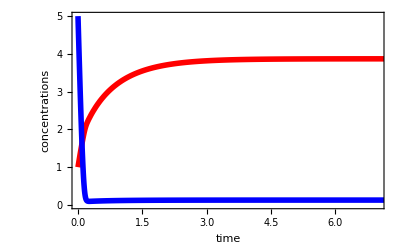

```mathematica
Plot[Evaluate[{x[t],y[t]}/.tsol],{t,0,10},PlotRange->{{0,7},{0,5}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

Plot the rates

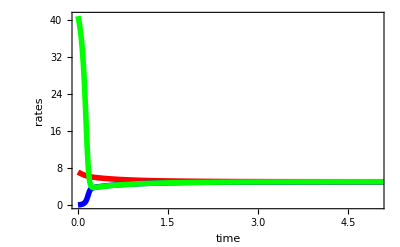

```mathematica
Plot[Evaluate[{v1,v2,v3}/.rateqs/.parm/.tsol],{t,0,10},PlotRange->{{0,5},All},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","rates"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]},{Green,Thickness[0.01]}}]
```

To calculate the steady state concentrations we will use the Mathematica function FindRoot which finds a solution to the steady state specification given initial conditions for the concentrations of the variable metabolite species.  One should always give initial conditions to findroot that are close to the steady state value and one way to do this is to obtain them from the time simulation. As at timepoint 5 the system is close to steady state, we choose the values at this time point.  We have to give initial conditions to FindRoot as {{x[t],1},{y[t],2}}.  This we can automate by,

```mathematica
Table[{vars[[i]][t],(vars[[i]][5]/.tsol)[[1]]},{i,1,Length[vars]}]
```

{{x[t],3.86498},{y[t],0.128414}}

The steady state equations are

```mathematica
Table[odes[[i]][[2]]==0,{i,1, Length[odes]}]/.rateqs/.parm
```

{(50 (1-x[t]/500))/(6+x[t])-(4 x[t] (1-y[t]/(5 x[t])))/(1+x[t]/5+10. y[t])==0,-(50 (1-0.005/y[t]) y[t])/(1.1+y[t])+(4 x[t] (1-y[t]/(5 x[t])))/(1+x[t]/5+10. y[t])==0}

FindRoot combines those two inputs to calculate the steady state

```mathematica
ss=FindRoot[Table[odes[[i]][[2]]==0,{i,1, Length[odes]}]/.rateqs/.parm,Table[{vars[[i]][t],(vars[[i]][5]/.tsol)[[1]]},{i,1,Length[vars]}]]
```

{x[t]→3.86992,y[t]→0.128506}

The fluxes at steady state are

```mathematica
rateqs/.parm/.ss
```

{v1→5.02669,v2→5.02669,v3→5.02669}

Indeed they are all the same as expected and agree with the simulation

System properties of the model such as a concentration or flux depends in a complicated nonlinear fashion on kinetic parameters to make those sensitivities explicit we will calculate sensitivity coefficients.  We change all the parameters by 1% and determine the % change in the concentrations and rates of the metabolic pathway at steady state.  This means we have to make the calculation of the time dependent solution with NDSolve and the steady state with FindRoot parameter dependent.

```mathematica
parmchange[param_,newvalue_]:=ReplacePart[parm,Position[parm,param][[1]][[1]]->param->newvalue]
```

```mathematica
tsolchange[param_,newvalue_]:=NDSolve[Join[odes/.rateqs/.parmchange[param,newvalue],init],vars,{t,0,100}]
```

```mathematica
sschange[param_,newvalue_]:=FindRoot[Table[odes[[i]][[2]]==0,{i,1, Length[odes]}]/.rateqs/.parmchange[param,newvalue],Table[{vars[[i]][t],(vars[[i]][5]/.tsolchange[param,newvalue])[[1]]},{i,1,Length[vars]}]]
```

Now we can for instance determine the dependency of the steady state flux through the metabolic pathway as function of the maximal rate of enzyme 1.

{{1.,0.798268},{3.5,2.44506},{6.,3.65543},{8.5,4.57254},{11.,5.29903},{13.5,5.89622},{16.,6.40129},{18.5,6.83786},{21.,7.22169},{23.5,7.56374},{26.,7.87193},{28.5,8.15213},{31.,8.40882},{33.5,8.64551},{36.,8.86495},{38.5,9.0694},{41.,9.26067},{43.5,9.44028},{46.,9.60951},{48.5,9.76942},{51.,9.92094},{53.5,10.0648},{56.,10.2018},{58.5,10.3325},{61.,10.4573},{63.5,10.5768},{66.,10.6913},{68.5,10.8013},{71.,10.907},{73.5,11.0088},{76.,11.1068},{78.5,11.2014},{81.,11.2928},{83.5,11.3811},{86.,11.4665},{88.5,11.5493},{91.,11.6294},{93.5,11.7072},{96.,11.7827},{98.5,11.856}}

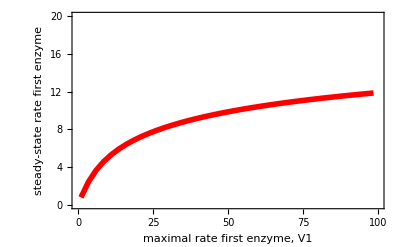

```mathematica
Table[{i,v1/.rateqs/.parmchange[V1,i]/.sschange[V1,i]},{i,1,100,2.5}]
ListPlot[%,Joined->True,PlotRange->{{0,100},{0,20}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"maximal rate first enzyme, V1","steady-state rate first enzyme"},PlotStyle->{{Red,Thickness[0.01]}}]
```

Determining the sensitvity coefficients 

Example calculation

```mathematica
sschange[V1,1.01*V1/.parm] (* new steady state *)
sschange[V1,V1/.parm] (* reference steady state *)
((x[t]/.%%)-(x[t]/.%))/(x[t]/.%)(* fractional change in x[t] *)
```

{x[t]→3.91208,y[t]→0.129278}

{x[t]→3.86992,y[t]→0.128506}

0.0108953

```mathematica
onepercup=Table[{parm[[i]][[1]],((x[t]/.sschange[parm[[i]][[1]],1.01*parm[[i]][[2]]])-(x[t]/.sschange[parm[[i]][[1]],parm[[i]][[2]]]))/(x[t]/.sschange[parm[[i]][[1]],parm[[i]][[2]]])},
{i,1,Length[parm]}];
onepercdown=Table[{parm[[i]][[1]],((x[t]/.sschange[parm[[i]][[1]],0.99*parm[[i]][[2]]])-(x[t]/.sschange[parm[[i]][[1]],parm[[i]][[2]]]))/(x[t]/.sschange[parm[[i]][[1]],parm[[i]][[2]]])},
{i,1,Length[parm]}];
```

```mathematica
TableForm[onepercup]
TableForm[onepercdown]
```

V1 | 0.0108953
K1s | -0.00534065
Keq1 | 0.0000841793
K1x | 0.00425803
V2 | -0.00742083
K2x | 0.00557645
Keq2 | -0.0000495508
K2y | -0.00311995
V3 | -0.00338426
K3y | 0.00305004
Keq3 | -0.000136827
K3p | -0.000275156
s | 0.00544645
p | 0.000415949

V1 | -0.0109026
K1s | 0.00541523
Keq1 | -0.0000858656
K1x | -0.00428891
V2 | 0.00755135
K2x | -0.00560679
Keq2 | 0.0000505505
K2y | 0.00316955
V3 | 0.0034432
K3y | -0.00306281
Keq3 | 0.00013958
K3p | 0.000280608
s | -0.00547904
p | -0.00041614

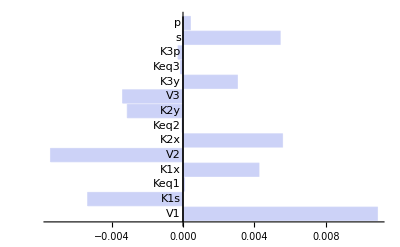

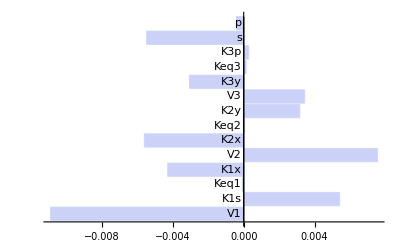

```mathematica
BarChart[onepercup[[All,2]],ChartLabels->Table[ToString[parm[[i]][[1]]],{i,1,Length[parm]}],BarOrigin->Left,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16}]

BarChart[onepercdown[[All,2]],ChartLabels->Table[ToString[parm[[i]][[1]]],{i,1,Length[parm]}],BarOrigin->Left,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16}]
```

So clearly some parameters have a larger effect on the steady state concentration of metabolite concentration X than others.

We can also use manipulate to study the model dynamics.  If you want be able to vary all parameters with sliders then you can do it as follows

```mathematica
tsolmanipulate[s_,V1_,K1s_,K1x_,Keq1_,V2_,K2x_,Keq2_,K2y_,V3_,K3y_,Keq3_,K3p_,x0_,y0_,p_]:=NDSolve[{x'[t]==(s V1 (1-x[t]/(Keq1 s)))/(K1s (1+s/K1s+x[t]/K1x))-(V2 x[t] (1-y[t]/(Keq2 x[t])))/(K2x (1+x[t]/K2x+y[t]/K2y)),y'[t]==-(V3 (1-p/(Keq3 y[t])) y[t])/(K3y (1+p/K3p+y[t]/K3y))+(V2 x[t] (1-y[t]/(Keq2 x[t])))/(K2x (1+x[t]/K2x+y[t]/K2y)),x[0]==x0,y[0]==y0},{x,y},{t,0,20}]
```

```mathematica
Manipulate[Block[{sol},
sol=tsolmanipulate[s,V1,K1s,K1x,Keq1,V2,K2x,Keq2,K2y,V3,K3y,Keq3,K3p,x0,y0,p];
GraphicsGrid[{{Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,10},PlotRange->{{0,7},{0,10}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},PlotLabel->"x is red; y is blue"]},{Plot[Evaluate[{((V1*s)/K1s(1-x[t]/(s Keq1)))/(1+s/K1s+x[t]/K1x),((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)}/.sol],{t,0,10},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","rates"},PlotLabel->"v1 is red, v2 is blue, v3 is green",PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]},{Green,Thickness[0.01]}},PlotRange->{{0,7},{0,20}}]}}]],
{{V1,10},1,20},
{{K1s,1},0.1,10},
{{Keq1,100},1,1000},
{{K1x,1},0.1,10},
{{V2,10},1,20},
{{K2x,1},0.1,10},
{{K2y,1},0.1,10},
{{Keq2,10},1,1000},
{{V3,10},1,20},
{{K3y,1},0.1,10},
{{K3p,5},0.1,10},
{{Keq3,10},1,1000},
{{s,1},0.1,10},
{{p,0.1},0.1,10},
{{x0,1},0.1,20},
{{y0,5},0.1,20}]
```

ReplaceAll::reps: {tsolmanipulate[1,10,1,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,10.,1.,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[1,13.76,1,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,13.76,1.,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[1,1.18,1,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,1.18,1.,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[1,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[1,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[1,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[1,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[1.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1,100,10,1,10,1,10,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tsolmanipulate[10.,1.18,9.37,1.,100.,10.,1.,10.,1.,10.,«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.